```mathematica
AppendTo[$Path,"C:\\Users\\User\\git\\nilostep\\mma-notebooks"];
```

```mathematica
<<Geometry`
```

```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

GraphJoin::shdw: Symbol GraphJoin appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphProduct::shdw: Symbol GraphProduct appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphSum::shdw: Symbol GraphSum appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

SetDelayed::write: Tag TreeQ in TreeQ[g_Graph] is Protected.

```mathematica
fn[n_]:=Map[Times@@#&,Flatten[Values[GroupBy[Map[#+1&,IntegerPartitions[n]],Length]],1]]
```

```mathematica
fn[5]
```

{6,10,12,16,18,24,32}

```mathematica
IntegerPartitions[5]
Map[#+1&,IntegerPartitions[5]]
GroupBy[Map[#+1&,IntegerPartitions[5]],Length]
Values[GroupBy[Map[#+1&,IntegerPartitions[5]],Length]]
Flatten[Values[GroupBy[Map[#+1&,IntegerPartitions[5]],Length]],1]
Map[Times@@#&,Flatten[Values[GroupBy[Map[#+1&,IntegerPartitions[5]],Length]],1]]
```

{{5},{4,1},{3,2},{3,1,1},{2,2,1},{2,1,1,1},{1,1,1,1,1}}

{{6},{5,2},{4,3},{4,2,2},{3,3,2},{3,2,2,2},{2,2,2,2,2}}

<|1→{{6}},2→{{5,2},{4,3}},3→{{4,2,2},{3,3,2}},4→{{3,2,2,2}},5→{{2,2,2,2,2}}|>

{{{6}},{{5,2},{4,3}},{{4,2,2},{3,3,2}},{{3,2,2,2}},{{2,2,2,2,2}}}

{{6},{5,2},{4,3},{4,2,2},{3,3,2},{3,2,2,2},{2,2,2,2,2}}

{6,10,12,16,18,24,32}

```mathematica
nnFactorList[n_]:=Module[
{fac,len,tab,set,ssp,spt,lst},
fac=FactorInteger[n];
len=Length[fac];
tab=Table[Array[fac[[k,1]]&,fac[[k,2]]],{k,1,len}];
set=Flatten[tab,1];
ssp=SetPartitions[set];
spt=Map[Sort[#]&,ssp]//DeleteDuplicates;
lst=Map[Map[Times@@#&,#]&,spt];
lst
]
```

```mathematica
nnFactorList[2^4]//Length
nnFactorList[2^3 3]//Length
nnFactorList[2^2 3^2]//Length
nnFactorList[2^2 3 5]//Length
nnFactorList[2 3 5 7]//Length
```

5

7

9

11

15

```mathematica
nnFactorList[2^5]//Length
nnFactorList[2^4 3]//Length
nnFactorList[2^3 3^2]//Length
nnFactorList[2^3 3 5]//Length
nnFactorList[2^2 3^2 5]//Length
nnFactorList[2^2 3 5 7]//Length
nnFactorList[2 3 5 7 11]//Length
```

7

12

16

21

26

36

52

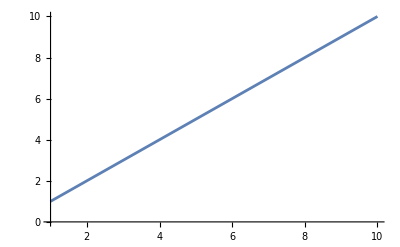

```mathematica
Plot[x,{x,1,10}]
```

```mathematica
numDivs[k_]:=Length[Divisors[k]]
numDivsL[n_]:=ListPlot[Table[numDivs[k],{k,1,n}]]
numDivsD[n_]:=DiscretePlot[numDivs[k],{k,1,n}]
```

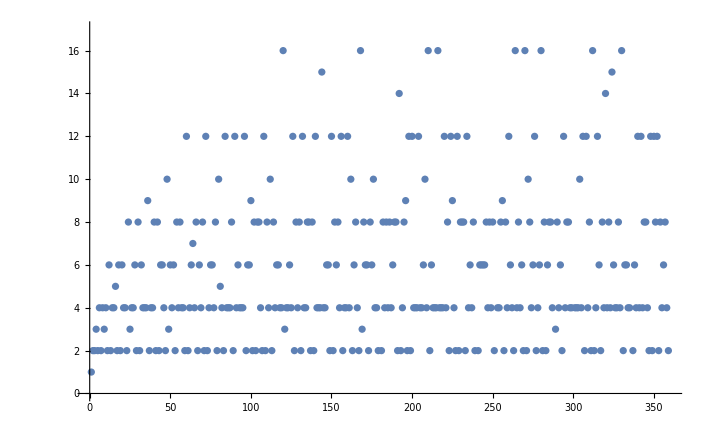

```mathematica
numDivsL[360]
```

```mathematica
Table[numDivs[k],{k,230,250}]
```

{8,8,8,2,12,4,6,4,8,2,20,2,6,6,6,6,8,4,8,4,8}

```mathematica
PartitionsP[2^10]
```

61847822068260244309086870983975